## Inizialization

```mathematica
(*Quit[];*)
```

```mathematica
(*Get["C:\\Users\\fsiano\\work\\dev\\workspace\\LeastSquaresMonteCarlo\\LeastSquaresMonteCarlo.m"]*)
```

```mathematica
1+1
```

2

## Deal 0_4

```mathematica
<|"label"->"0_4", "description"->"31 days - start 0 - end 5 - full 10 - inj/wit 1 - storage inventory fixed for 2 days", "definition"->{31, (-1&) & /@ Range[31], (1&) & /@ Range[31],Interval[{0,0}], Interval[{5,5}],Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[26]]} |>
```

```mathematica
feasibleRange[31, (-1&) & /@ Range[31], (1&) & /@ Range[31],Interval[{0,0}], Interval[{5,5}],Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[26]]]
```

{Interval[{0,0}],Interval[{0,1}],Interval[{0,2}],Interval[{1,3}],Interval[{2,2}],Interval[{2,2}],Interval[{1,3}],Interval[{0,4}],Interval[{0,5}],Interval[{0,6}],Interval[{0,7}],Interval[{0,8}],Interval[{0,9}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{1,9}],Interval[{2,8}],Interval[{3,7}],Interval[{4,6}],Interval[{5,5}]}

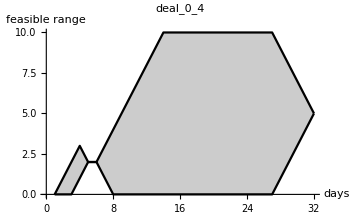

```mathematica
plotFeasibilityRange["0_4","",{31, (-1&) & /@ Range[31], (1&) & /@ Range[31],Interval[{0,0}], Interval[{5,5}],Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[26]]},350,{}][[2]]
```

```mathematica
makeInventoryMeshOneStep["Decisions"][{0, 1.5, 8.9}, -5 &, 2 &, 0, 10, {1, 2}, 0.01]
```

{0,1,1.5,2,2.5,3.5,3.9,8.9,9.9,10}

```mathematica
makeAllowedActions[{0,1.5}, -5 , 2 , 0, 10, 3, 0.1]
```

{{0,1,2},{0.,1.75,3.5}}

```mathematica
makeInventoryMesh["NominalDelta"][31, (-1&) & /@ Range[31], (1&) & /@ Range[31],Interval[{0,0}], Interval[{5,5}],Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[26]], 0.5, 10^-2]
```

{{0},{0,1/2,1},{0,1/2,1,3/2,2},{1,3/2,2,5/2,3},{2},{2},{1,3/2,2,5/2,3},{0,1/2,1,3/2,2,5/2,3,7/2,4},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{0,1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10},{1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9},{2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8},{3,7/2,4,9/2,5,11/2,6,13/2,7},{4,9/2,5,11/2,6},{5}}

```mathematica
makeInventoryMesh["Decisions"][31, (-1&) & /@ Range[31], (1&) & /@ Range[31],Interval[{0,0}], Interval[{5,5}],Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[25], {Interval[{5, 5}]}], {3, 3}, 10^-2]
```

{{0,1/3,2/3,1},{0,1/3,2/3,1},{0,1/3,2/3,1,4/3,5/3,2},{1,4/3,5/3,2,7/3,8/3,3},{2},{2},{1,4/3,5/3,2,7/3,8/3,3},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{0,1/3,2/3,1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10},{1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9},{2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8},{3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7},{4,13/3,14/3,5,16/3,17/3,6}}

```mathematica
makeInventoryMeshOneStep["Decisions"][{2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8}, -1 &, 1 &,0, 6,{3, 3}, 10^-2]
```

{1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8}

```mathematica
makeInventoryMeshOneStep["Decisions"][{2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8}, -1 &, 1 &,0, 4.99,{3, 3}, 10^-2]
```

{1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,4.99}

## Deal 0_8

```mathematica
<|"label"->"0_8", "description"->"10 days - start 0 - end 7 - full 10 - wit 1 - inj variable - storage inventory fixed for 2 days", "definition"->{10, (-1 &) & /@ Range[10], Join[(1 &) & /@ Range[6],(2 &) & /@ Range[4]],Interval[{0,0}], Interval[{7,7}], Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[4], {Interval[{7,7}]}]} |>
```

```mathematica
feasibleRange[10, (-1 &) & /@ Range[10], Join[(1 &) & /@ Range[6],(2 &) & /@ Range[4]],Interval[{0,0}], Interval[{7,7}], Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[4], {Interval[{7,7}]}]]
```

{Interval[{0,0}],Interval[{0,1}],Interval[{0,2}],Interval[{1,3}],Interval[{2,2}],Interval[{2,2}],Interval[{1,3}],Interval[{1,5}],Interval[{3,7}],Interval[{5,8}],Interval[{7,7}]}

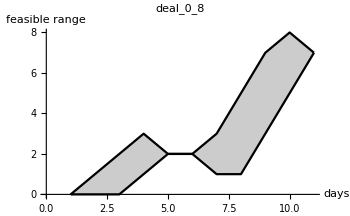

```mathematica
plotFeasibilityRange["0_8","",{10, (-1 &) & /@ Range[10], Join[(1 &) & /@ Range[6],(2 &) & /@ Range[4]],Interval[{0,0}], Interval[{7,7}], Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[4], {Interval[{7,7}]}]},350,{}][[2]]
```

```mathematica
makeInventoryMesh["NominalDelta"][10, (-1 &) & /@ Range[10], Join[(1 &) & /@ Range[6],(2 &) & /@ Range[4]],Interval[{0,0}], Interval[{7,7}], Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[4], {Interval[{7,7}]}], 0.5, 10^-2]
```

{{0},{0,1/2,1},{0,1/2,1,3/2,2},{1,3/2,2,5/2,3},{2},{2},{1,3/2,2,5/2,3},{1,3/2,2,5/2,3,7/2,4,9/2,5},{3,7/2,4,9/2,5,11/2,6,13/2,7},{5,11/2,6,13/2,7,15/2,8},{7}}

```mathematica
makeInventoryMesh["Decisions"][10, (-1 &) & /@ Range[10], Join[(1 &) & /@ Range[6],(2 &) & /@ Range[4]],Interval[{0,0}], Interval[{7,7}], Join[Interval[{0,10}] & /@ Range[3], Interval[{2,2}] & /@ Range[2], Interval[{0,10}] & /@ Range[4], {Interval[{7,7}]}], {3,3}, 10^-2]
```

{{0},{0,1/3,2/3,1},{0,1/3,2/3,1,4/3,5/3,2},{1,4/3,5/3,2,7/3,8/3,3},{2},{2},{1,4/3,5/3,2,7/3,8/3,3},{1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5},{3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7},{5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8},{7}}

```mathematica
makeAllowedActions[{0,1/3,2/3,1}, -1& , 2& , 0, 2, 3,10^-2]
```

{{0,1,2},{0,1,2},{0,1,2},{0,1,2}}

```mathematica
basisFunctions["poly"][4, {2., 3. , 4.}]
```

{{1.,2.,4.,8.,16.},{1.,3.,9.,27.,81.},{1.,4.,16.,64.,256.}}

```mathematica
basisFunctions["poly"][4, {2., 3. , 4.}]
```

{{1.,2.,4.,8.,16.},{1.,3.,9.,27.,81.},{1.,4.,16.,64.,256.}}

```mathematica
With[{data = RandomVariate[NormalDistribution[0, 1],10^5]},
makeMatrix["poly"][4, data] ; //AbsoluteTiming
]
```

{0.023,Null}

```mathematica
Module[{data = RandomVariate[NormalDistribution[0, 1],10^5]},
makeMatrix["poly"][4, data] ; //AbsoluteTiming
]
```

{0.019,Null}

```mathematica
Module[{data = RandomVariate[NormalDistribution[0, 1],10^5]},
data=Transpose[{data, Range[Length[data]]}];
DesignMatrix[data, {x,x^2,x^3,x^4}, x] ; //AbsoluteTiming
]
```

{0.07601,Null}

```mathematica
Remove[dm]
dm=Compile[{{order, _Integer}, {sims, _Real, 1}},
DesignMatrix[Transpose[{sims, Range[Length[sims]]}],x^#&/@Range[1,order],x],
CompilationTarget->"C"
]
```

CompiledFunction[…]

```mathematica
dm[4, {2., 3., 4.}]
```

{{1.,2.,4.,8.,16.},{1.,3.,9.,27.,81.},{1.,4.,16.,64.,256.}}

```mathematica
Module[{data = RandomVariate[NormalDistribution[0, 1],10^5]},
(*data=Transpose[{data, Range[Length[data]]}];*)
dm[4, data] ; //AbsoluteTiming
]
```

{0.10101,Null}

```mathematica
Module[{data = RandomVariate[NormalDistribution[0, 1],10^5]},
(*data=Transpose[{data, Range[Length[data]]}];*)
dm[4, data] ; //AbsoluteTiming
]
```

{0.10401,Null}

```mathematica
Module[{data = RandomVariate[NormalDistribution[0, 2],10^5]},
Dot[PseudoInverse[makeMatrix["poly"][4, data], Tolerance->Automatic], RandomVariate[NormalDistribution[0, 2],10^5]]  //AbsoluteTiming
]
```

{0.05601,{0.0109724,0.00193706,0.000155659,0.0000614811,-0.0000321201}}

## Deal 8

```mathematica
{365,(-5&)&/@Range[365],(5&)&/@Range[365],Interval[{0,0}],Interval[{0,0}],Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}]}
```

{365,{-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&},{5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&},Interval[{0,0}],Interval[{0,0}],{Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,0}]}}

```mathematica
feasibleRange[365,(-5&)&/@Range[365],(5&)&/@Range[365],Interval[{0,0}],Interval[{0,0}],Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}]]
```

{Interval[{0,0}],Interval[{0,5}],Interval[{0,10}],Interval[{0,15}],Interval[{0,20}],Interval[{0,25}],Interval[{0,30}],Interval[{0,35}],Interval[{0,40}],Interval[{0,45}],Interval[{0,50}],Interval[{0,55}],Interval[{0,60}],Interval[{0,65}],Interval[{0,70}],Interval[{0,75}],Interval[{0,80}],Interval[{0,85}],Interval[{0,90}],Interval[{0,95}],Interval[{0,100}],Interval[{0,105}],Interval[{0,110}],Interval[{0,115}],Interval[{0,120}],Interval[{0,125}],Interval[{0,130}],Interval[{0,135}],Interval[{0,140}],Interval[{0,145}],Interval[{0,150}],Interval[{0,155}],Interval[{0,160}],Interval[{0,165}],Interval[{0,170}],Interval[{0,175}],Interval[{0,180}],Interval[{0,185}],Interval[{0,190}],Interval[{0,195}],Interval[{0,200}],Interval[{0,205}],Interval[{0,210}],Interval[{0,215}],Interval[{0,220}],Interval[{0,225}],Interval[{0,230}],Interval[{0,235}],Interval[{0,240}],Interval[{0,245}],Interval[{0,250}],Interval[{0,255}],Interval[{0,260}],Interval[{0,265}],Interval[{0,270}],Interval[{0,275}],Interval[{0,280}],Interval[{0,285}],Interval[{0,290}],Interval[{0,295}],Interval[{0,300}],Interval[{0,305}],Interval[{0,310}],Interval[{0,315}],Interval[{0,320}],Interval[{0,325}],Interval[{0,330}],Interval[{0,335}],Interval[{0,340}],Interval[{0,345}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,345}],Interval[{0,340}],Interval[{0,335}],Interval[{0,330}],Interval[{0,325}],Interval[{0,320}],Interval[{0,315}],Interval[{0,310}],Interval[{0,305}],Interval[{0,300}],Interval[{0,295}],Interval[{0,290}],Interval[{0,285}],Interval[{0,280}],Interval[{0,275}],Interval[{0,270}],Interval[{0,265}],Interval[{0,260}],Interval[{0,255}],Interval[{0,250}],Interval[{0,245}],Interval[{0,240}],Interval[{0,235}],Interval[{0,230}],Interval[{0,225}],Interval[{0,220}],Interval[{0,215}],Interval[{0,210}],Interval[{0,205}],Interval[{0,200}],Interval[{0,195}],Interval[{0,190}],Interval[{0,185}],Interval[{0,180}],Interval[{0,175}],Interval[{0,170}],Interval[{0,165}],Interval[{0,160}],Interval[{0,155}],Interval[{0,150}],Interval[{0,145}],Interval[{0,140}],Interval[{0,135}],Interval[{0,130}],Interval[{0,125}],Interval[{0,120}],Interval[{0,115}],Interval[{0,110}],Interval[{0,105}],Interval[{0,100}],Interval[{0,95}],Interval[{0,90}],Interval[{0,85}],Interval[{0,80}],Interval[{0,75}],Interval[{0,70}],Interval[{0,65}],Interval[{0,60}],Interval[{0,55}],Interval[{0,50}],Interval[{0,45}],Interval[{0,40}],Interval[{0,35}],Interval[{0,30}],Interval[{0,25}],Interval[{0,20}],Interval[{0,15}],Interval[{0,10}],Interval[{0,5}],Interval[{0,0}]}

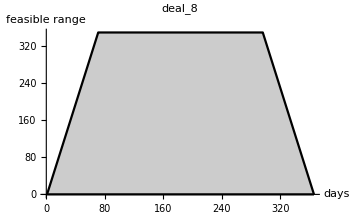

```mathematica
plotFeasibilityRange["8","",{365,(-5&)&/@Range[365],(5&)&/@Range[365],Interval[{0,0}],Interval[{0,0}],Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}]},350,{}][[2]]
```

```mathematica
makeInventoryMesh["NominalDelta"][365, (-5&)&/@Range[365],(5&)&/@Range[365],Interval[{0,0}],Interval[{0,0}],Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}],4, 10^-1]
```

{{0},{0,5},{0,5,10},{0,15/4,15/2,45/4,15},{0,4,8,12,16,20},{0,25/6,25/3,25/2,50/3,125/6,25},{0,15/4,15/2,45/4,15,75/4,45/2,105/4,30},{0,35/9,70/9,35/3,140/9,175/9,70/3,245/9,280/9,35},{0,4,8,12,16,20,24,28,32,36,40},{0,45/11,90/11,135/11,180/11,225/11,270/11,315/11,360/11,405/11,450/11,45},347,{0,4,8,12,16,20,24,28,32,36,40},{0,35/9,70/9,35/3,140/9,175/9,70/3,245/9,280/9,35},{0,15/4,15/2,45/4,15,75/4,45/2,105/4,30},{0,25/6,25/3,25/2,50/3,125/6,25},{0,4,8,12,16,20},{0,15/4,15/2,45/4,15},{0,5,10},{0,5},{0}}
 |  |  |  |

```mathematica
discretiseIntervals[Interval[{0.,2.}, {8, 10.6}], 2.4, Abs[#1-#2]<0.01 &] // Chop
```

{0,2.,8,9.3,10.6}

```mathematica
discretiseIntervals[Interval[{0.,2.}, {8, 10.6}], 2.4, same[#1, #2, 0, 0.1] &]
```

{-2.22507×10^-308,2.,8,9.3,10.6}

```mathematica
discretiseIntervals[Interval[{0.,2.}, {5., 5.}, {8, 10.6}], 2.4, same[#1, #2, 0, 0.1] &]
```

{-2.22507×10^-308,2.,5.,8,9.3,10.6}

```mathematica
discretiseIntervals[Interval[{0.,2.}, {5., 5.}, {8, 10.6}], 0.4, same[#1, #2, 0, 0.1] &]
```

{-2.22507×10^-308,0.333333,0.666667,1.,1.33333,1.66667,2.,5.,8,8.37143,8.74286,9.11429,9.48571,9.85714,10.2286,10.6}

```mathematica
discretiseIntervals[Interval[{0., 10}], 4, 0.1]
```

{-2.22507×10^-308,3.33333,6.66667,10}

```mathematica
discretiseIntervals[Interval[{0.,2.}, {8, 8.6}], 0.3, 10^-1]
```

{0.,0.285714,0.571429,0.857143,1.14286,1.42857,1.71429,2.,8.,8.3,8.6}

```mathematica
discretiseIntervals[Interval[{0.,2.}, {8, 8.6}], 0.3, 1]
```

{0.,1.14286,8.}

```mathematica
meshtol=makeInventoryMesh["NominalDelta"][365, (-5&)&/@Range[365],(5&)&/@Range[365],Interval[{0,0}],Interval[{0,0}],Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}],2.5, 10^-1];
```

```mathematica
Length@Flatten@meshtol
```

41666

```mathematica
discretiseIntervals[Interval[{0,0}], (Max[Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}][[1]]]-Min[Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}][[1]]])/10^-1,10^-1]
```

{0}

```mathematica
Module[{nT,minRate, maxRate,startInv, endInv, invBounds, nDecisions, tolerance, feaRange,mesh},
nT=365;
minRate=(-0.5 &) & /@ Range[nT];
maxRate=(0.7 &) & /@ Range[nT];
startInv=Interval[{0,0}];
endInv=Interval[{0,0}];
invBounds=Join[Interval[{0,200}] & /@ Range[nT-1], {Interval[{0,0}]}];
nDecisions = 3;
tolerance = 10^-1;
feaRange=feasibleRange[nT, minRate, maxRate,startInv,endInv, invBounds];
mesh=NestList[{#[[1]]+1,makeInventoryMeshOneStep["Tolerance"][#[[2]],minRate[[#[[1]]+1]], maxRate[[#[[1]]+1]],Min[feaRange[[#[[1]]+1]]],Max[feaRange[[#[[1]]+1]]], nDecisions, tolerance]} &,{0, discretiseIntervals[startInv,Max[tolerance, (Max[startInv]-Min[endInv])/tolerance],tolerance]}, 5][[2;;, 2]]
]
```

{{0},{0,0.233333,0.466667,0.7},{0,0.133333,0.3,0.466667,0.7,0.933333,1.16667,1.4},{0,0.133333,0.3,0.433333,0.6,0.766667,0.9,1.06667,1.23333,1.4,1.63333,1.86667,2.1},{0,0.133333,0.266667,0.4,0.533333,0.666667,0.833333,1.,1.13333,1.3,1.46667,1.6,1.76667,1.93333,2.1,2.33333,2.56667,2.8}}

```mathematica
meshDec=makeInventoryMesh["Decisions"][365,(-5&)&/@Range[365],(5&)&/@Range[365],Interval[{0,0}],Interval[{0,0}],Join[Interval[{0,350}]&/@Range[364],{Interval[{0,0}]}],{2, 2},0.1];
```

```mathematica
Length@Flatten@meshDec
```

41666

## Junk

```mathematica
testDeals
```

label | description | definition
0_4 | 31 days - start 0 - end 5 - full 10 - inj/wit 1 - storage inventory fixed for 2 days | { 31,{-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&},⋯_4 }
0_8 | 10 days - start 0 - end 7 - full 10 - wit 1 - inj variable - storage inventory fixed for 2 days | { 10,{-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&},{1&,1&,1&,1&,1&,1&,2&,2&,2&,2&},⋯_3 }
8 | 365 days - start 0 - end 0 - full 350 - inj/wit 5 | { 365,{-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,«251»,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&,-5&},{5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,«213»,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&,5&},Interval[{0,0}],Interval[{0,0}],{Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],«340»,Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,350}],Interval[{0,0}]} }
3 levels | 3rows |  | Dataset[{__Association}]

```mathematica
adeal=testDeals[Select[#label=="0_4" &]][1]
```

label | 0_4
description | 31 days - start 0 - end 5 - full 10 - inj/wit 1 - storage inventory fixed for 2 days
definition | { 31,{-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&},⋯_4 }
2 levels | 3rows | Dataset[<|"label" -> _, "description" -> _, "definition" -> _|>]

```mathematica
plotFeasibilityRange[Sequence@@ Values[Normal[adeal]],350,{}]
```

{31 days - start 0 - end 5 - full 10 - inj/wit 1 - storage inventory fixed for 2 days,-Graphics-}

```mathematica
adeal["definition"]
```

{ 31,{-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&,-1&},⋯_4 }
1 level | 6elementsDataset[_List]

```mathematica
adeal["definition"][[1]]
```

31
0 levels | 0elementsDataset[_]

```mathematica
spot=testSpot[[1;;Normal@adeal["definition"][[1]], All]];
```

```mathematica
spot//Dimensions
```

{31,100}

```mathematica
feasibleRange[Sequence@@Normal[adeal["definition"]]]
```

{Interval[{0,0}],Interval[{0,1}],Interval[{0,2}],Interval[{1,3}],Interval[{2,2}],Interval[{2,2}],Interval[{1,3}],Interval[{0,4}],Interval[{0,5}],Interval[{0,6}],Interval[{0,7}],Interval[{0,8}],Interval[{0,9}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{0,10}],Interval[{1,9}],Interval[{2,8}],Interval[{3,7}],Interval[{4,6}],Interval[{5,5}]}